-Graphics-
By Ryan Bell for Wolfram Summer School 2020.

Constructing directed graphs of email conversations
Abstract: InboxGraph is a property graph representation of mail server archive data, in which message collections are presented in a higher-dimensional space than is possible with traditional user interfaces with linear timestamped constraints. RFC-822 message parsing is used to extract message trajectories between servers and network participants, forming a metadata-rich lattice of vertices and edges inside a directed graph. Asymmetrical relationships between participants are used to calculate Address Rank measurements of information flow importance and to partition the graph into best-fitting communities, opening new channels for organizational optimization. Additional layers of natural language processing and data export to open formats permit further interactive exploration, querying, and discovery of deeper associations within the graph.

Section 1. Community partitioning & Time series helpers 
Linear time series subgraph construction and best-fitting community functions.

```mathematica
(*GetGraphPartitionGroups returns the best-fitting subgroup partitioning for a collection of overlapping groups.*)
GetGraphPartitionGroups[subgroups_List]:=Module[{uniqueItems,e,g,p},
(*GetOccurLength returns the number of subgroups co-occurances.*)
GetOccurLength[groups_,{i_,j_}]:=Count[ContainsAll[#,{i,j}]&/@groups,True];

uniqueItems=Flatten[subgroups]//DeleteDuplicates;

(*Construct graph partitioning edges for subgroups using co-occurance counts.*)
e=DeleteCases[
If[
Unequal@@#,
{UndirectedEdge@@#,GetOccurLength[subgroups,#]},
Nothing
]&/@Subsets[uniqueItems,{2}],
{_,0}
];

(*Construct graph using co-occurences as edge weights.*)
g=Graph[e[[All,1]],EdgeWeight->e[[All,2]],VertexLabels->Automatic,EdgeLabels->"EdgeWeight"];

(*Add remaining isolated subgroups.*)
g=VertexAdd[g,Complement[uniqueItems,VertexList[g]]];

(*Partition by edge weight sum minimization.*)
p=If[Length[#]>1,FindGraphPartition[Subgraph[g,#]],{#}]&/@ConnectedComponents[g];
Join@@p
]

(*BuildLinkedGraph creates a directed linear list of vertices with optional tooltips*)
Options[BuildLinkedGraph]={"ShowTooltip"->False};
BuildLinkedGraph[v_List,OptionsPattern[]]:=(
Graph[v,MapIndexed[v[[#2[[1]]]]->#1&,v[[2;;]]],
VertexLabels->{
#->If[OptionValue["ShowTooltip"],Placed[#,Tooltip],#]
}&/@v]//Flatten
)
```

Section 2. Directed InboxGraph visualization.
Visualize a MBOX archive thread flow diagram.
(Example uses a mailing list archive from https://lists.apache.org.) 

-Graphics-

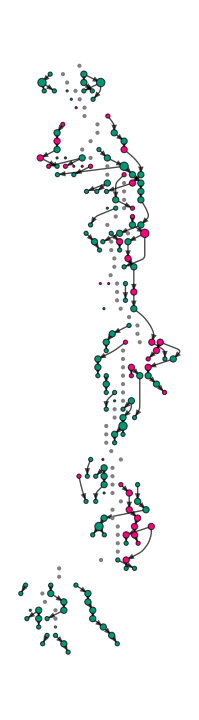

```mathematica
(*BuildInboxGraph creates a directed graph using message identifiers and originating dates with graph partition coloring by subgraph address participation.*)
Options[BuildInboxGraph]={"FilePath"->SystemDialogInput["FileOpen"],"UseTimeSeries"->True,"ShowTimeSeries"->False,"VertexSizeRange"->{0.25,1.0}};
BuildInboxGraph[OptionsPattern[]]:=(
(*Fields to import.*)
fields={
"MessageID",
"OriginatingDate",
"Subject",
"Body",
"ReplyToMessageID",
"FromAddress",
"ToAddressList",
"CcAddressList",
"BccAddressList",
"ReplyToAddressList"
};

(*Import mailbox.*)
mboxData=<||>;
AssociateTo[
mboxData,
(*Key by MessageID.*)
(#[[1]]->AssociationThread[fields,#])&/@Transpose[Import[OptionValue["FilePath"],{"MBOX",fields}]]
];

(*Add NLP Feature Engineering: Sentiment classification.*)
mboxData=AssociationMap[#[[1]]->Join[#[[2]],<|"Sentiment"->Classify["Sentiment",#[[2]]["Body"]]|>]&,mboxData];

(*Build time series backbone.*)
vDates=DateObject[#,"Day"]&/@Sort[DeleteDuplicates[#[fields[[2]]]&/@Values[mboxData]]]//DeleteDuplicates;
eDates=MapIndexed[vDates[[#2[[1]]]]->#1&,vDates[[2;;]]];
sDates=MapIndexed[vDates[[#2[[1]]]]->0.0&,vDates[[2;;]]];
vDatesColors=MapIndexed[vDates[[#2[[1]]]]->Gray&,vDates[[2;;]]];
vDatesShapes=MapIndexed[
vDates[[#2[[1]]]]->If[
OptionValue["ShowTimeSeries"], (*Optional time series backbone visualization.*)
"Circle",
None
]&,vDates[[2;;]]
];

(*Build message thread edges.*)
vMsgs=Keys[mboxData];
lMsgs=Flatten[{#->Placed[mboxData[#],Tooltip]}&/@vMsgs];
eMsgs=Values[Map[#ReplyToMessageID->#MessageID&,Select[mboxData,#ReplyToMessageID=!=None&&MemberQ[vMsgs,#ReplyToMessageID]&]]];
gMsgs=Graph[vMsgs,eMsgs];

(*Connect message vertices to relevant time series anchor vertices.*)
eMsgDates=Flatten[{DateObject[mboxData[#][fields[[2]]],"Day"]->#}&/@vMsgs];

(*Calculate message importance by Vertex Degree*)
g=Graph[vMsgs,eMsgs];
sMsgs=KeyValueMap[#->#2&,
AssociationThread[
VertexList[g],
(*Scale values using VertexSizeRange parm.*)
Rescale[VertexDegree[gMsgs]]*
(OptionValue["VertexSizeRange"][[2]]-OptionValue["VertexSizeRange"][[1]])+
OptionValue["VertexSizeRange"][[1]]
]
];

(*GetParticipants returns all of the participants for a given list of messageIDs.*)
GetParticipants[msgIDs_]:= (
Flatten[Select[
Values[KeySelect[mboxData[#], MemberQ[Select[fields,StringContainsQ[#,"Address"]&],#] &]]//Flatten,
StringQ (*Validate address formatting.*)
]&/@msgIDs]//DeleteDuplicates
);

(*Partition community by subgraph co-occurance edge weight minimization.*)
communitySubgroups=GetGraphPartitionGroups[
GetParticipants/@WeaklyConnectedComponents[g] 
];

(*Perceptually-uniform palette generation with Lightness/Chroma/Hue selection.*)
communitySubgroupColors = Map[LCHColor[0.5,1,#/Length[communitySubgroups]]&,Range[Length[communitySubgroups]]];

(*Create a lookup table for each address color.*)
communityAddressToColor=<||>;
AssociateTo[
communityAddressToColor,
Flatten[
MapIndexed[
Function[
{community, communityIdx},
 {#->communitySubgroupColors[[communityIdx[[1]]]]}&/@community
][#1, #2]&,
communitySubgroups
]
]
];

(*Color by the most common community participation on a message.*)
vMsgsColors=KeyValueMap[#->#2&,
AssociationThread[vMsgs,
Commonest[
Flatten[communityAddressToColor/@GetParticipants[{#}]]
][[1]]&/@vMsgs
]
];

(*Construct inbox graph.*)
v=vMsgs;
l=lMsgs;
e=eMsgs;
s=sMsgs;
c=vMsgsColors;

If[OptionValue["UseTimeSeries"],
(*Anchor messages to a linear time series backbone.*)
v=Join[vDates,v];
c=Join[vDatesColors,c];
e=Join[eDates, eMsgDates, e];
s=Join[sDates,s];
];

(*Color message thread routing with optional time series visualization.*)
edgeStyle=If[
MatchQ[#[[1]],_DateObject],
#->If[OptionValue["ShowTimeSeries"],Gray, Transparent],
#->If[OptionValue["ShowTimeSeries"],Blue, Black]
]&/@e;

Graph[v,e,VertexLabels->l,VertexSize->s,VertexStyle->c,VertexShapeFunction->vDatesShapes, EdgeStyle->edgeStyle,GraphLayout->"LayeredDigraphEmbedding"]
)

(*Render InboxGraph visualization.*)
BuildInboxGraph[UseTimeSeries->True,ShowTimeSeries->False]
```

Section 3. AddressRank visualization.
Calculating the page rank centrality score for addresses and link by max message destination volume.

-Graphics-
(https://en.wikipedia.org/wiki/PageRank#/media/File:PageRank-hi-res.png)

PageRank is a graph analysis algorithm which measures the relative importance of vertices within a directed graph using the number of edge links it receives, the propensity (out-going edges) of the linkers, and the PageRank centrality of the linkers.

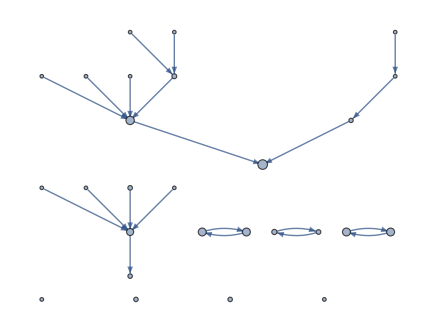

```mathematica
(*BuildAddressRankGraph visualizes the information flow edges between addresses by max destination volume and Page Rank centrality.*)
Options[BuildAddressRankGraph]={"FilePath"->SystemDialogInput["FileOpen"]};
BuildAddressRankGraph[OptionsPattern[]]:=(
(*Import mailbox.*)
fields={"FromAddress","ToAddressList", "CcAddressList", "BccAddressList", "ReplyToAddressList"};
mbox=Import[OptionValue["FilePath"],{"MBOX",fields}];

(*Key by FromAddress.*)
msgDeliveries={#[[1]], Select[Flatten[#[[2;;]]],StringQ]}&/@Transpose[mbox];

(*Tally the number of messages between unique participants.*)
msgTally=Select[
Tally[Flatten[Map[Function[msg,{msg[[1]]->#}&/@msg[[2]]],
msgDeliveries]]],
#[[1]][[1]]≠#[[1]][[2]]& (*Ignore self-directed messages.*)
];
msgTallyGroups=Normal[GroupBy[{#[[1]][[1]],#[[1]][[2]],#[[2]]}&/@msgTally,First]];

(*Construct AddressRankGraph*)
v=DeleteDuplicates[Flatten[msgDeliveries]];
l=Flatten[{#->Placed[#,Tooltip]}&/@v];
e=Flatten[{#[[1]]->Sort[#[[2]],#1[[3]]>#2[[3]]&][[1,2]]}&/@msgTallyGroups]; (*Edge by destination volume.*)
ePageRank=#[[1]]&/@msgTally;(* All messaging edges.*)
s=AssociationThread[v,Rescale[PageRankCentrality[Graph[v,ePageRank],0.85]]*.25+.15]//Normal;

Graph[v,e,VertexLabels->l,VertexSize->s,GraphLayout->"LayeredDigraphEmbedding"]
)

(*Render AddressRank visualization.*)
BuildAddressRankGraph[]
```